```mathematica
distr00b={{1,88.6},{3,88.1},{5,85.9},{7,85.1},{9,83.5},{11,83.1},{13,81.4},{15,79.2},{17,79},{19,76.3},{21,74.3},{23,73.4},{25,71.4},{27,68.4},{29,68.8},{31,67.8},{33,63},{35,64.3},{37,61.9},{39,59.6},{41,59.3},{43,58.4},{45,58},{47,55.4},{49,51.4},{51,47.5},{53,46.9},{55,48.7},{57,443.4},{59,43.6},{61,43.5},{63,42.2},{65,42.7},{67,41.6},{69,39.9},{71,39.8},{73,39.2},{74,40.5}};Pt1=C1 Exp[-t/T2]+C3;
```

```mathematica
fit1=FindFit[distr00b,Pt1,{C1,T2,C3},t]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{C1→1.70472×10^8,T2→5.33479×10^8,C3→-1.70472×10^8}

```mathematica
modelf1=Function[{t},Evaluate[Pt1/.fit1]]
```

Function[{t},-1.70472×10^8+1.70472×10^8 ⅇ^(-1.87449×10^-9 t)]

```mathematica
Error1=1/38 Sum[(-1.70472*10^8+1.70472*10^8 ⅇ^(-1.874489*10^-9 distr00b⟦i⟧⟦1⟧)-distr00b⟦i⟧⟦2⟧)^2,{i,1,38}]//Simplify
```

11048.5

```mathematica
Error1=1/38 Sum[84.7931* Exp[-0.00433558*distr00b⟦i⟧⟦1⟧]-distr00b⟦i⟧⟦2⟧,{i,1,38}]
```

0.00643778

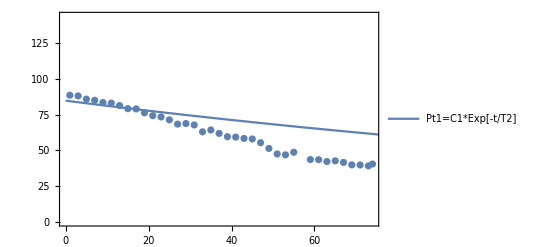

```mathematica
Show[ListPlot[distr00b],Plot[fit1[t],{t,0,80},PlotLegends->{ "Pt1=C1*Exp[-t/T2]"}],Frame->True]
```

```mathematica
Pt2=C2 Exp[-(t/T2b)^2]+C4;
fit2=NonlinearModelFit[distr00b,Pt2,{C2,T2b,C4},t]
```

FittedModel[80.1676 ⅇ^(-0.000056425 t^2)]

```mathematica
Error2=1/38 Sum[80.1676 *Exp[-0.000056425*(distr00b⟦i⟧⟦1⟧)^2]-distr00b⟦i⟧⟦2⟧,{i,1,38}]
```

0.0224408

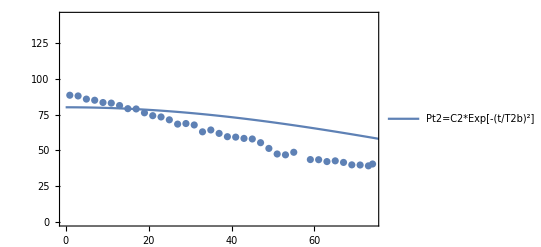

```mathematica
Show[ListPlot[distr00b],Plot[fit2[t],{t,0,80},PlotLegends->{ "Pt2=C2*Exp[-(t/T2b)^2]"}],Frame->True]
```

```mathematica
(* Pt3= C3*t + b *)
```

```mathematica
fit3=LinearModelFit[distr00b,t,t]
```

FittedModel[84.3739-0.319548 t]

```mathematica
Error3=1/38 Sum[84.3739-0.3195478*distr00b⟦i⟧⟦1⟧-distr00b⟦i⟧⟦2⟧,{i,1,38}]
```

0.0000190684

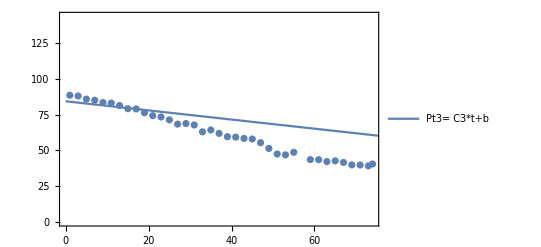

```mathematica
Show[ListPlot[distr00b],Plot[fit3[t],{t,0,80},PlotLegends->{ "Pt3= C3*t+b"}],Frame->True]
```

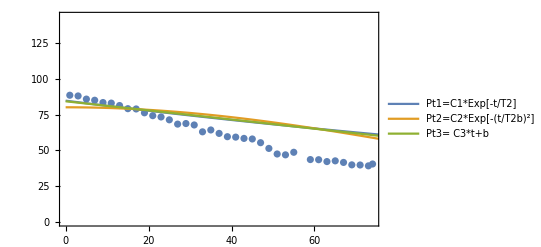

```mathematica
Show[ListPlot[distr00b],Plot[{fit1[t],fit2[t],fit3[t]},{t,0,80},PlotLegends->{ "Pt1=C1*Exp[-t/T2]","Pt2=C2*Exp[-(t/T2b)^2]","Pt3= C3*t+b"}],Frame->True]
```